```mathematica
a=({{1, 0, 0, 0, 0, 0, 0, 0, 0}, {((10000/h)((((-3/40)(10)+3)/h)+(3/80))), (-(20000/h^2)((-3/40)(10)+3)), ((10000/h)((-3/80)+(((-3/40)(10)+3)/h))), 0, 0, 0, 0, 0, 0}, {0, ((10000/h)((((-3/40)(10)+3)/h)+(3/80))), (-(20000/h^2)((-3/40)(10)+3)), ((10000/h)((-3/80)+(((-3/40)(10)+3)/h))), 0, 0, 0, 0, 0}, {0, 0, ((10000/h)((((-3/40)(10)+3)/h)+(3/80))), (-(20000/h^2)((-3/40)(10)+3)), ((10000/h)((-3/80)+(((-3/40)(10)+3)/h))), 0, 0, 0, 0}, {0, 0, 0, ((10000/h)((((-3/40)(10)+3)/h)+(3/80))), (-(20000/h^2)((-3/40)(10)+3)), ((10000/h)((-3/80)+(((-3/40)(10)+3)/h))), 0, 0, 0}, {0, 0, 0, 0, ((10000/h)((((-3/40)(10)+3)/h)+(3/80))), (-(20000/h^2)((-3/40)(10)+3)), ((10000/h)((-3/80)+(((-3/40)(10)+3)/h))), 0, 0}, {0, 0, 0, 0, 0, ((10000/h)((((-3/40)(10)+3)/h)+(3/80))), (-(20000/h^2)((-3/40)(10)+3)), ((10000/h)((-3/80)+(((-3/40)(10)+3)/h))), 0}, {0, 0, 0, 0, 0, 0, ((10000/h)((((-3/40)(10)+3)/h)+(3/80))), (-(20000/h^2)((-3/40)(10)+3)), ((10000/h)((-3/80)+(((-3/40)(10)+3)/h)))}, {0, 0, 0, 0, 0, 0, (((10000)(1.5))/(2h)), (-((20000)(1.5))/h), (((30000)(1.5))/(2h))}})
```

{{1,0,0,0,0,0,0,0,0},{(10000 (3/80+9/(4 h)))/h,-45000/h^2,(10000 (-3/80+9/(4 h)))/h,0,0,0,0,0,0},{0,(10000 (3/80+9/(4 h)))/h,-45000/h^2,(10000 (-3/80+9/(4 h)))/h,0,0,0,0,0},{0,0,(10000 (3/80+9/(4 h)))/h,-45000/h^2,(10000 (-3/80+9/(4 h)))/h,0,0,0,0},{0,0,0,(10000 (3/80+9/(4 h)))/h,-45000/h^2,(10000 (-3/80+9/(4 h)))/h,0,0,0},{0,0,0,0,(10000 (3/80+9/(4 h)))/h,-45000/h^2,(10000 (-3/80+9/(4 h)))/h,0,0},{0,0,0,0,0,(10000 (3/80+9/(4 h)))/h,-45000/h^2,(10000 (-3/80+9/(4 h)))/h,0},{0,0,0,0,0,0,(10000 (3/80+9/(4 h)))/h,-45000/h^2,(10000 (-3/80+9/(4 h)))/h},{0,0,0,0,0,0,7500./h,-30000./h,22500./h}}

```mathematica
b=({{0}, {-50}, {-50}, {-50}, {-50}, {-50}, {-50}, {-50}, {0}})
```

{{0},{-50},{-50},{-50},{-50},{-50},{-50},{-50},{0}}

```mathematica
(*let*)h=.1
```

0.1

```mathematica
LinearSolve[a,b]
```

{{-7.35473×10^-19},{0.000164574},{0.000307438},{0.000428519},{0.000527746},{0.000605044},{0.000660341},{0.000693564},{0.000704638}}

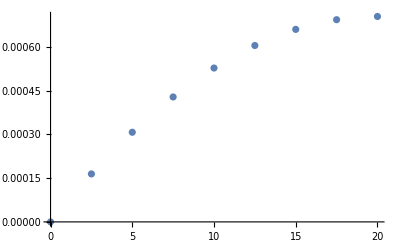

```mathematica
ListPlot[{{0,0},{2.5,0.0001645737050079316},{5,0.00030743758376658594},{7.5,0.00042851914937696634},{10,0.0005277456729137029},{12.5,0.0006050441826169502},{15,0.0006603414630815881},{17.5,0.0006935640544437148},{20,0.0007046382515644236}},PlotRange->All]
```